# Constructing a curve along a surface

## Start with a surface and a 2D parametric curve

```mathematica
surface=Plot3D[x^2+y^2,{x,-2,2},{y,-2,2},PlotRange->{-1,4},BoxRatios->Automatic,ClippingStyle->None]
```

-Graphics3D-

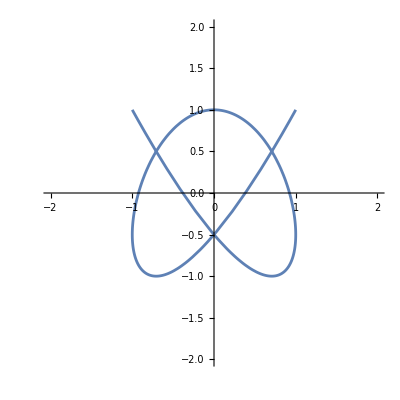

```mathematica
ParametricPlot[{Sin[3t],Cos[4t]},{t,Pi/2,3Pi/2},PlotRange->{-2,2}]
```

## Convert the 2D parametric curve to a 3D parametric curve by computing the third coordinate using the function from the surface

```mathematica
curve3D=ParametricPlot3D[{Sin[3t],Cos[4t],Sin[3t]^2+Cos[4t]^2},{t,Pi/2,3Pi/2},PlotRange->{{-2,2},{-2,2},{-1,4}},BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
dg=DiscretizeGraphics[curve3D]
```

-Graphics3D-

```mathematica
thickened=Graphics3D[Tube[MeshCoordinates[dg],.1]]
```

-Graphics3D-

```mathematica
Show[thickened,surface]
```

-Graphics3D-